```mathematica
Clear["Global`*"];
a:=2;
Remove[ffund,orthDeriv];
ffund:=Log[(##[[1]]^2+##[[2]]^2)^(1/2)]&;
orthDeriv[f_,xy_]:={-D[f[{x,y}],y],D[f[{x,y}],x]}/.{x->xy[[1]],y->xy[[2]]};
deriv[f_,xy_]:={D[f[{x,y}],x],D[f[{x,y}],y]}/.{x->xy[[1]],y->xy[[2]]};
e1:={1,0};
Remove[x,y];
```

```mathematica
Options[plotRegionStream]={interval1->{-1,1},a1->2,noInflow1->False,levelFunction->None};
plotRegionStream[u_,psi_,OptionsPattern[]]:=With[{interval=OptionValue[interval1],
a=OptionValue[a1],
noInflow=OptionValue[noInflow1],
f=OptionValue[levelFunction]},(
plotRegion=ImplicitRegion[-a<x<a&&-a<y<a&&interval[[1]]<=psi[{x,y}]<=interval[[2]],{x,y}];
(*pr=plotRegion[plotRegion];*)
plts = {StreamPlot[u[{x,y}],{x,y}∈plotRegion, StreamPoints->Fine,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, RegionFunction->(interval[[1]]<psi[{#1,#2}]<interval[[2]]&),
RegionFillingStyle->LightGray,RegionBoundaryStyle->None,StreamColorFunction->"GrayTones"]};
boundaryFunc =({D[psi[{dx,dy}],dx],D[psi[{dx,dy}],dy]}/.{dx:>##[[1]],dy:>##[[2]]}).u[##]&;
sigmaRegions=Table[ImplicitRegion[-a<=x<=a&&-a<=y<=a&&symb[boundaryFunc[{x,y}]],{x,y}],{symb,{LessThan[0],GreaterThan[0]}}];
(*plot boundaries*)
If[noInflow,
AppendTo[plts,Table[ContourPlot[psi[{x,y}]==level,{x,-a,a},{y,-a,a},ContourStyle->{Black,Opacity[0.5]}],
{level,interval}]];
AppendTo[plts,Table[ContourPlot[Max[Abs[x],Abs[y]]==a,{x,-a,a},{y,-a,a},ContourStyle->{Black,Opacity[0.5]}],
{level,interval}]],
AppendTo[plts, Table[Table[ContourPlot[psi[{x,y}]==level,{x,y}∈params[[1]],ContourStyle->{params[[2]],Opacity[0.5]}],{params,{{sigmaRegions[[1]],Blue},{sigmaRegions[[2]],Red}}}],
{level,interval}]]];
(*plot critical points*)
zeros=(NSolve[u[{x,y}]==0&&{x,y}∈plotRegion,{x,y,z},Reals])[[All,All,2]];
AppendTo[plts,ListPlot[zeros,PlotStyle->{Black,PointSize[0.04]}]];
(*plot contours*)
If[f===None,,
AppendTo[plts,ContourPlot[f[{x,y}],{x,y}∈plotRegion,Contours->f@Transpose[zeros],ContourStyle->Dashed,Mesh->None,ContourShading->None]]];
p=Show[plts];
p=Legended[p,Placed[LineLegend[{Red,Black,Blue,{Black,Dashed}},{"Σ^+","Σ^0","Σ^-","level set"}],After]];
p=Legended[p,Placed[PointLegend[{Black},{"critical point"}],After]]
);
p
]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

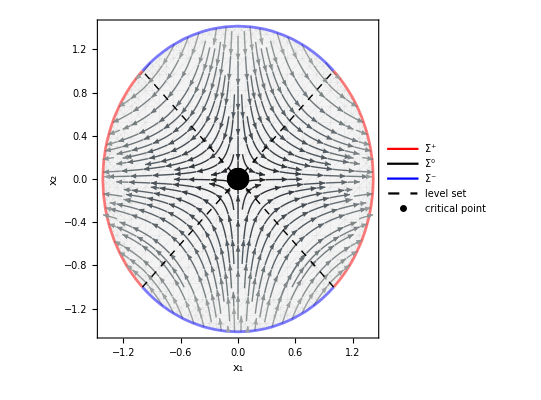

```mathematica
f6=##[[1]]^2-##[[2]]^2&;
u6=deriv[f6,##]&;
levelCircle=##[[1]]^2+##[[2]]^2&;
plotRegionStream[u6,levelCircle,interval1->{-4,2},levelFunction->f6]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

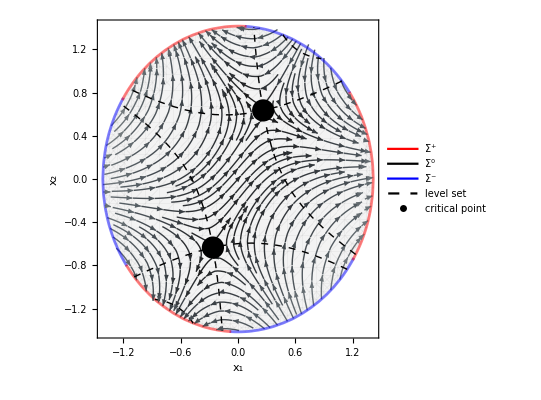

```mathematica
f7=##[[1]]^3-3##[[1]]*##[[2]]^2+##[[1]]+##[[2]] &;
u7=deriv[f7,##]&;
plotRegionStream[u7,levelCircle,interval1->{-4,2},levelFunction->f7]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

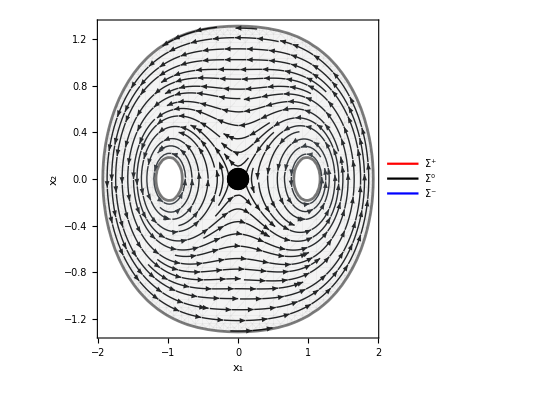

```mathematica
psi1:=ffund[##-e1]+ffund[##+e1]&;
u1:=orthDeriv[psi1,##] &;
plotRegionStream[u1,psi1,noInflow1->True]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

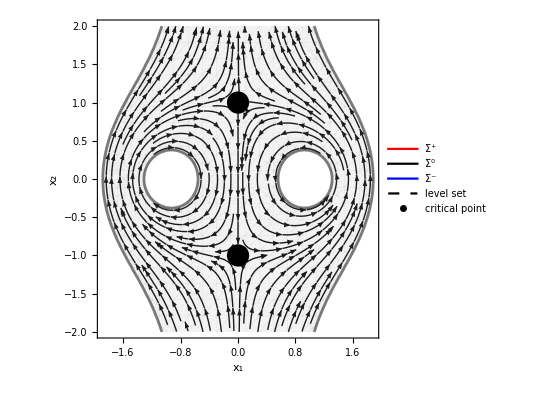

```mathematica
psi2:=ffund[##-e1]-ffund[##+e1]+##[[1]]&;
u2:=orthDeriv[psi2,##] &;
plotRegionStream[u2,psi2,noInflow1->True,interval1->{-0.7,0.7}]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

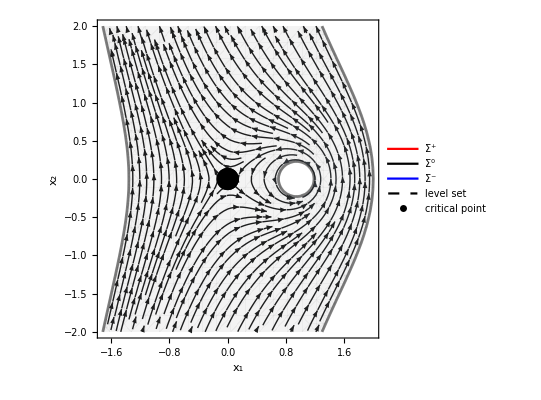

```mathematica
psi3:=ffund[##-e1]+##[[1]]&;
u3:=orthDeriv[psi3,##] &;
plotRegionStream[u3,psi3,noInflow1->True,interval1->{-0.5,2}]
```

```mathematica
Animate[StreamPlot[(1-lambda)*g1[{x,y}]+lambda*g2[{x,y}],{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```

```mathematica
Animate[VectorPlot[(1-lambda)*g1[{x,y}]4+lambda*g2[{x,y}],{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, VectorPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```

```mathematica
regionOmega=RegionDifference[Disk[{0,0},4],RegionUnion[Disk[{-2,0},1],Disk[{2,0},1]]];
solveDirichlet[uBoundary_]:=With[{LaplaceEquation2D={Laplacian[u[x,y],{x,y}]==0, DirichletCondition[u[x,y]==uBoundary[x,y],True]}},(
NDSolveValue[LaplaceEquation2D,u,{x,y}∈regionOmega][##[[1]],##[[2]]]&)]

uBoundary1=If[#1^2+#2^2>15,0,1]&;
psi4=solveDirichlet[uBoundary1];
u4=orthDeriv[psi4,##]&;
```

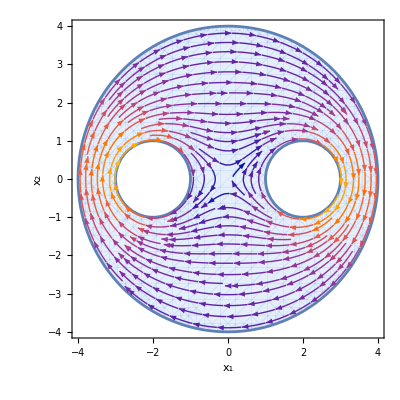

```mathematica
StreamPlot[Evaluate[u4[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine]
```

```mathematica
uBoundary2=If[#1^2+#2^2>15,0,If[#1>0,-1,1]]&;
f5=solveDirichlet[uBoundary2];
g5=orthDeriv[f5,##]&;
```

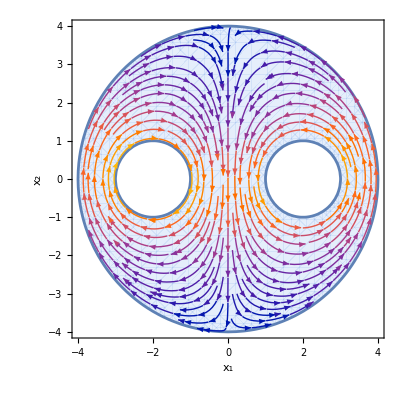

```mathematica
StreamPlot[Evaluate[g5[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine]
```

```mathematica
Animate[StreamPlot[Evaluate[(1-lambda)*g4[{x,y}]+lambda*g5[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```